# Mechanics of Solids Project

```mathematica
ClearAll["Global'*"]
```

## Simplified Model of the Aircraft wing

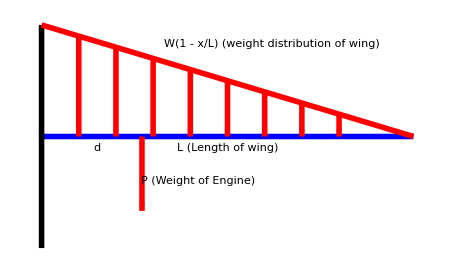

```mathematica
Graphics[{
 AbsoluteThickness[4], Blue, Line[{{0, 0}, {10, 0}}],  (* Horizontal line from (0,0) to (10,0) *)
 Red, Arrow[{{2.7, 0}, {2.7, -2}}],         (* Downward-pointing arrow at (2,0) *)
 Thick, Black, Line[{{0, 3}, {0, -3}}], (* Support for the cantilver beam *)
 Thick, Red, Line[{{0, 3}, {10, 0}}],
 Red, Arrow[{{1, 2.7}, {1, 0}}],
 Red, Arrow[{{2, 2.4}, {2, 0}}],
 Red, Arrow[{{3, 2.1}, {3, 0}}],
 Red, Arrow[{{4, 1.8}, {4, 0}}],
 Red, Arrow[{{5, 1.5}, {5, 0}}],
 Red, Arrow[{{6, 1.2}, {6, 0}}],
 Red, Arrow[{{7, 0.9}, {7, 0}}],
 Red, Arrow[{{8, 0.6}, {8, 0}}],
 Black,Text["P (Weight of Engine) ",{4.2, -1.2}],
 Black,Text["d",{1.5, -.3}],
 Black,Text["L (Length of wing)",{5, -.3}],
 Black,Text[" W(1 - x/L) (weight distribution of wing)  ",{6.2, 2.5}],
}]
```

Parameters we have chosen for our Problem are :- 

1)  d (distance between hinge and the engine);
2 )P is the weight of the engine;
3)  wo*(1 - x/L)  weight distribution of the wings ;
4) E is the Young's modulus;
5) I is the moment of inertia of the beam;

```mathematica
g = 10; (* Acceleration due to gravity*)
P = 7.55*10^3 * g; (*Weight of the engine of an Airbus A350 in Kgs)*)
wo = 12.5*10^3 * g;  (* Example value for wo *)
L = 32;  (* Length of wing of an Airbus A350 in meters *)
d = 10;  (* Example value for d *)
E1 = 69*10^9; (* Young's modulus *)
I1 = 10000;  (* Moment of inertia *)
```

## Shear Force Diagram

```mathematica
The Shear force is a piecewise function which is represented as following;
for x < d;
v[x_]:= -P - (wo*(L-x)^2)/(2*L)

for x > d;
v[x_]:= -(wo*(L-x)^2)/(2*L)
```

```mathematica
Ploting the shear force diagram;
L1 = L;
v[x_] := Piecewise[{{-P - (wo*(L-x)^2)/(2*L), x < d},{-(wo*(L-x)^2)/(2*L), x > d}}]
Graph1 = Manipulate[Plot[v[x], {x, 0, L},PlotStyle->{Red,Thick,Thickness[0.005]},
	PlotRange -> All, AxesLabel -> {"x", "v(x)"},
	PlotLabel -> Style["Shear Force Diagram", 20, Bold,Italic], GridLines->Automatic,
	Frame->True,
	FrameLabel -> {Style["x (m)", 20,Italic], Style["Shear Force (N)", 15, Italic]},
	PlotTheme->"Classic", ImageSize->510, Filling->Top],{L,5,L1}];
Graph1
```

## Bending Moment Diagram

```mathematica
The Bending Moment is a continuous function which is represented as following;
for x < d;
M1[x_]:= -P(x-d) - (wo*(L-x)^3)/(6*L)

for x > d;
M1[x_]:= -(wo*(L-x)^3)/(6*L)
```

```mathematica
Ploting the Bending Moment diagram;

M1[x_] := Piecewise[{{-P(x-d) - (wo*(L-x)^3)/(6*L), x < d},{-(wo*(L-x)^3)/(6*L), x > d}}]
Graph2 = Manipulate[Plot[M1[x], {x, 0, L},PlotStyle->{Blue,Thick,Thickness[0.005]},
	PlotRange -> All, AxesLabel -> {"x", "M(x)"},
	PlotLabel -> Style["Bending moment Diagram", 20, Bold,Italic], GridLines->Automatic,
	Frame->True,
	FrameLabel -> {Style["x (m)", 20,Italic], Style["Bending Moment (N-m)", 15, Italic]},
	PlotTheme->"Classic", ImageSize->510, Filling->Top],{L,5,L1}];
Graph2
```

## Deflection in the beam and its deformed configuration

```mathematica
(*(* Define constants *)
EI = 1;  (* Replace with actual EI value *)
L = 10;  (* Beam length *)
wo = 5;  (* Load intensity *)
P = 10;  (* Point Load *)
d = 4;   (* Load position *)

(* Define bending moment function *)
M1[x_] := Piecewise[{
   {-P (x - d) - (wo*(L - x)^3)/(6*L), x < d},
   {-(wo*(L - x)^3)/(6*L), x > d}
}];

(* Solve the differential equation *)
vSol = DSolve[{v''[x] == M1[x]/EI, v'[0] == 0, v[0] == 0}, v[x], x];

(* Display the solution *)
vSol // Simplify
*)
```

```mathematica
(*(* Define the function for deflection v(x) - using downward as negative convention*)
δ[x_] := -(1/(E1 I1)) * ((P x^2 / 6) * (3 L - x) + (M x^2 / 2));

(* Plot the function within the beam length 0 <= x <= L *)
Plot[v[x], {x, 0, L}, 
  AxesLabel -> {"x (position)", "Deflection v(x)"},
  PlotStyle -> {Thick, Blue}, 
  GridLines -> Automatic, 
PlotRange -> {{0, L}, {-0.00001, 0}}, 
  Frame -> True, 
  FrameLabel -> {"x (position)", "Deflection v(x)"},AspectRatio->1]*)
```

```mathematica
(*(* Define parameters *)
P = 10; (* Example load value *)
M = 5;  (* Example moment value *)
L = 10; (* Beam length *)
(* Define the function for deflection v(x) - using downward as negative convention*)
δ[x_] := -(1/(E1 I1)) * ((P x^2 / 6) * (3 L - x) + (M x^2 / 2));

(* Plot the function within the beam length 0 <= x <= L *)
Plot[v[x], {x, 0, L}, 
  AxesLabel -> {"x (position)", "Deflection v(x)"},
  PlotStyle -> {Thick, Blue}, 
  GridLines -> Automatic, 
PlotRange -> {{0, L}, {-0.00001, 0}}, 
  Frame -> True, 
  FrameLabel -> {"x (position)", "Deflection v(x)"},AspectRatio->1]*)
```